# Cubic splines

```mathematica
ClearAll["Global`*"]
```

### Basis functions

Determine the basis functions by solving the appropriate linear system:

```mathematica
poly[x_]=Sum[Subscript[a, i] x^i,{i,0,3}]
```

a_0+x a_1+x^2 a_2+x^3 a_3

```mathematica
coef=CoefficientList[poly[x],x]
```

{a_0,a_1,a_2,a_3}

```mathematica
h00[x_]=poly[x]/.First[Solve[{poly[0]==1,poly[1]==0,poly'[0]==0,poly'[1]==0},coef]];
```

```mathematica
h01[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==1,poly'[0]==0,poly'[1]==0},coef]];
```

```mathematica
h10[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==1,poly'[1]==0},coef]];
```

```mathematica
h11[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==1},coef]];
```

Expressions of the basis functions:

```mathematica
TableForm[Map[#&,{h00[x],h01[x],h10[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | 1-3 x^2+2 x^3
h01 | 3 x^2-2 x^3
h10 | x-2 x^2+x^3
h11 | -x^2+x^3

Their first derivatives:

```mathematica
TableForm[Map[D[#,x]&,{h00[x],h01[x],h10[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | -6 x+6 x^2
h01 | 6 x-6 x^2
h10 | 1-4 x+3 x^2
h11 | -2 x+3 x^2

Plots of the basis functions:

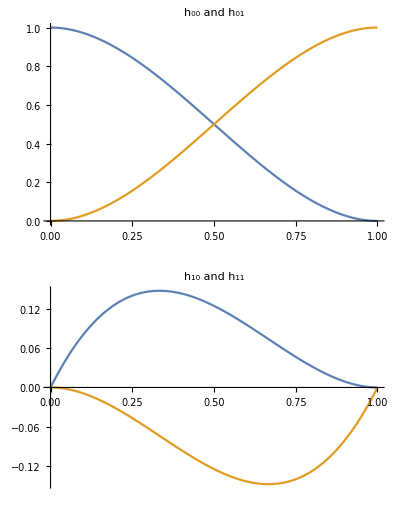

```mathematica
GraphicsColumn[{Plot[{h00[x],h01[x]},{x,0,1},PlotLabel->"h_00 and h_01"],Plot[{h10[x],h11[x]},{x,0,1},PlotLabel->"h_10 and h_11"]}]
```

Their first derivatives:

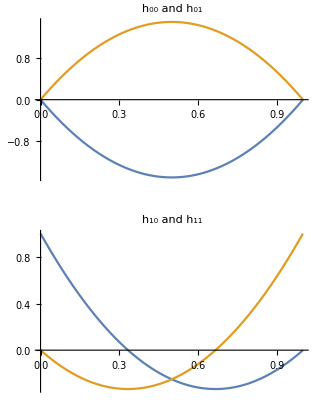

```mathematica
GraphicsColumn[{Plot[Evaluate[{h00'[x],h01'[x]}],{x,0,1},PlotLabel->"h_00 and h_01"],Plot[Evaluate[{h10'[x],h11'[x]}],{x,0,1},PlotLabel->"h_10 and h_11"]}]
```

### Interpolation function

The interpolating function over [0, 1] is a linear combination of those six basis functions:

```mathematica
h[x_,y0_,y1_,s0_,s1_]=y0*h00[x]+y1*h01[x]+s0*h10[x]+s1*h11[x];
```

```mathematica
Manipulate[GraphicsColumn[{Plot[h[x,y0,y1,s0,s1],{x,0,1},PlotRange->{{0,1},{-2,2}},PlotLabel->"Cubic spline function"],Plot[Evaluate[D[h[x,y0,y1,s0,s1],x]],{x,0,1},PlotRange->{{0,1},{-10,10}},PlotLabel->"First derivative"]}],{{y0,-1},-2,2},{{y1,1},-2,2},{{s0,0},-2,2},{{s1,0},-2,2}]
```

We can extend this function to an arbitrary interval using an affine transformation:

```mathematica
f[x_]=y0*h00[(x-x0)/(x1-x0)]+y1*h01[(x-x0)/(x1-x0)]+s0*(x1-x0)*h10[(x-x0)/(x1-x0)]+s1*(x1-x0)*h11[(x-x0)/(x1-x0)];
```

Check that the function and its derivatives have the right values:

```mathematica
f[x0]
```

y0

```mathematica
f[x1]
```

y1

```mathematica
f'[x0]
```

s0

```mathematica
f'[x1]
```

s1